# Equilibria extravaganza - let the diffusion begin

## 1 D Sanity check

In this section i am looking at the Kimura famous 1 D diffusion, i calculate back V - which is the potential energy and then i will plug this in the Boltzmann distribution for the equilibria to verify
we indeed see the Wright equilibria-- which should coincide

```mathematica
b[x_]:= (x*(1-x))/Ne
```

```mathematica
D[b[x],x]
```

(1-x)/Ne-x/Ne

```mathematica
a[x_]:= (x*(1-x))/2* D[Log[W[x]],x] + u (1-x) - v x (*u: mutation [0] ->[1]. v: [1]->[0]]*)
```

```mathematica
(*Here comes the potential energy!*)
Vi[x_]:=Integrate[(D[b[x],x]- 2 a[x])/b[x] ,x]
```

```mathematica
Vi[t]/. t->0.5
```

-1.35857-100 Log[W[0.5]]

```mathematica
Z = NIntegrate[Exp[- 1*Vi[x]],{x,0,1}]
```

NIntegrate::zeroregion: Integration region {{1.,0.99999999999999999999999999997275243749960574466419003432897000423}} cannot be further subdivided at the specified working precision. NIntegrate assumes zero integral there and on any further indivisible regions.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.99999999999999810662305438375076468677767889263508772586860201548}. NIntegrate obtained 76.1333 and 0.652328 for the integral and error estimates.

76.1333

```mathematica
ρ[x_]:= Exp[- 1*Vi[x]]/Z
```

```mathematica
Simplify[Exp[- Vi[x]]/.x->0.5]
```

3.89062

so far so good, we have verified that theBoltaman distribution we get is indeed the Wright distribution

Lets see how much information we have accumulated and how much free fitness had accumulated!
For Miso's defintion of information we measure the KL divergenceU

```mathematica
u[x_]:= 1 (*the uniform distrbution over the unit interval*)
```

```mathematica
KLD=ResourceFunction["KullbackLeiblerDivergence"]; (*works like importing a library, D_KL isnt a regular built in mathematica function -- but darn
the domain here is the entire x axis and not just the unit line! *)
```

```mathematica
KLD[NormalDistribution[0,1],NormalDistribution[1,2]]
```

-1/4+Log[2]

```mathematica
Clear[KLInterval]
KLInterval[p_,q_]:=NIntegrate[p[x]*Log[p[x]/q[x]],{x,0,1}]
```

so, specifically for this case we will always the uniform distribution= the equilibrium under neutrality u(x)=1/(|Ω|)where Ω is the space we are at 
(either the HIlberts cube [0,1]^n or the simplex Δ^(2^n-1)) and |Ω| means its volume (this is =1 for [0,1]^n and 1/((n-1)!) for the (n-1) dimensional simplex ). Then we can pull |Ω| from the integral and we get a general expression
 up to the base of the log.

 To calculate the entropy we need to specify all of the parameters of the diffusion u,v,N and also how to fitness is determined.

```mathematica
Ne=100;
v= 0.0001 ;(*Miso had mu = v=u=0.0001!!*)
u=0.0001;
s= 0.00;
Ne s
```

0.

```mathematica
W[x_]:= (1+s) x +(1-x)
```

```mathematica
ρ[x]/.x->0.00000001
```

695856.

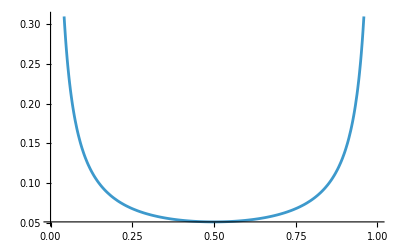

```mathematica
Plot[Evaluate[ρ[x]],{x,0.000000000,1}]
```

Sanity check lets make sure ρ integrates to 1

```mathematica
NIntegrate[ρ[x],{x,0,1}]
```

NIntegrate::zeroregion: Integration region {{1.,0.99999999999999999999999999997275243749960574466419003432897000423}} cannot be further subdivided at the specified working precision. NIntegrate assumes zero integral there and on any further indivisible regions.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.99999999999999810662305438375076468677767889263508772586860201548}. NIntegrate obtained 1. and 0.00856824 for the integral and error estimates.

1.

```mathematica
NIntegrate[Log[ρ[x]],{x,0,1}]
```

-2.37249

```mathematica
Z = NIntegrate[Exp[- Vi[x]],{x,0.0001,0.9999}] (*This is the [NOT!] free fitness score*)
```

3.02498×10^201

```mathematica
free_fitness[p_,Ne_,Vi_]:= -NIntegrate[ p[x]*Vi[x]/Ne,{x,0.000,1}]- NIntegrate[p[x]*Log[p[x]],{x,0.000,1}]
```

```mathematica
free_fitness[ρ,Ne,Vi]
```

free_fitness[ρ,100,Vi]

```mathematica
Vi[x]/.x->0.9999999
```

-15.7957

```mathematica
-NIntegrate[ ρ[x]*Evaluate[Vi[x]]/Ne,{x,0.00000001,0.9999999999}]- NIntegrate[ρ[x]*Log[ρ[x]],{x,0.000000001,0.99999999}]
-NIntegrate[ ρ[x]*Evaluate[Vi[x]]/Ne,{x,0.0000000,1}]- NIntegrate[ρ[x]*Log[ρ[x]],{x,0,1}]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.99999999981278613938470092815805626823414710424575702063521021046}. NIntegrate obtained -0.042802 and 1.42135×10^-6 for the integral and error estimates.

-1.98028

NIntegrate::zeroregion: Integration region {{1.,0.99999999999999999999999999997275243749960574466419003432897000423}} cannot be further subdivided at the specified working precision. NIntegrate assumes zero integral there and on any further indivisible regions.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.99999999999999810662305438375076468677767889263508772586860201548}. NIntegrate obtained -0.377093 and 0.00307704 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.9999465496780171902568325192905973608503700233995914459228515625}. NIntegrate obtained 36.6187 and 3.86034 for the integral and error estimates.

-36.2417

```mathematica
miso[p_] := -1*NIntegrate[p[x]*Log[2,p[x]],{x,0.00000,1}]
```

```mathematica
miso[ρ]
```

NIntegrate::zeroregion: Integration region {{1.,0.99999999999999999999999999997275243749960574466419003432897000423}} cannot be further subdivided at the specified working precision. NIntegrate assumes zero integral there and on any further indivisible regions.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.99999999999999810662305438375076468677767889263508772586860201548}. NIntegrate obtained 7.88786×10^301 and 7.20896×10^299 for the integral and error estimates.

NIntegrate::zeroregion: Integration region {{1.,0.99999999999999999999999999997275243749960574466419003432897000423}} cannot be further subdivided at the specified working precision. NIntegrate assumes zero integral there and on any further indivisible regions.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.99999999999999810662305438375076468677767889263508772586860201548}. NIntegrate obtained 7.88786×10^301 and 7.20896×10^299 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.99999999999999833552297401554899705442790134545403187354907677264}. NIntegrate obtained 5.93549 and 0.498144 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

-5.93549

So we are getting a negative result because we are taking continuous entropy, let us try to bin the distribution artificially to bins that are the width of 1/Ne

```mathematica
(*define p[x_] before this*)(*bin edges*)
nBins=Ne;
edges=Subdivide[0,1,nBins];

(*probability in each bin*)
pBins=Table[NIntegrate[ρ[x],{x,edges[[i]],edges[[i+1]]}],{i,1,nBins}];

(*normalize just in case of tiny numerical drift*)
pBins=pBins/Total[pBins];

(*discrete Shannon entropy of the bin distribution -- THIS SHOULD NOW BE POSITIVE AND HOPFULLY MATCH MISO'S RESULTS IN FIGURE 5A*)
Hbins=-Total[pBins*Log[pBins]]
```

NIntegrate::zeroregion: Integration region {{1.,0.99999999999999999999999999997275243749960574466419003432897000423}} cannot be further subdivided at the specified working precision. NIntegrate assumes zero integral there and on any further indivisible regions.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.99999999999999810662305438375076468677767889263508772586860201548}. NIntegrate obtained 7.88786×10^301 and 7.20896×10^299 for the integral and error estimates.

NIntegrate::zeroregion: Integration region {{1.,0.99999999999999999999999999997275243749960574466419003432897000423}} cannot be further subdivided at the specified working precision. NIntegrate assumes zero integral there and on any further indivisible regions.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.99999999999999810662305438375076468677767889263508772586860201548}. NIntegrate obtained 7.88786×10^301 and 7.20896×10^299 for the integral and error estimates.

NIntegrate::zeroregion: Integration region {{1.,0.99999999999999999999999999997275243749960574466419003432897000423}} cannot be further subdivided at the specified working precision. NIntegrate assumes zero integral there and on any further indivisible regions.

General::stop: Further output of NIntegrate::zeroregion will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.99999999999999810662305438375076468677767889263508772586860201548}. NIntegrate obtained 7.88786×10^301 and 7.20896×10^299 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

1.41622

OK now we are trying to get again MIso’s figure 5A, we rewrite the equilibrium as a function of both N and S.
and see whats the final information at equilibria is and also we see whats the free fitness as a function of both N and S.
BOth these cases now are for Haploids.

```mathematica
(*-----------------------------*)(*1) Model ingredients*)(*-----------------------------*)
ClearAll["Global`*"];

(*Domain clip to avoid log singularities exactly at 0,1*)
eps=10^-8;

(*Replace this with your fitness W(x,s) from your notebook*)
W[x_,s_]:=(1+s) x +(1-x) 

(*Parameters u,v are mutation rates;keep or replace as needed*)
u=10^-4;
v=10^-4;

(*Potential V(x;N,s) (edit to your exact formula/convention)*)
V[x_,Ne_,s_]:=- Ne Log[W[x,s]]+(1-2 Ne u) Log[x]+(1-2 Ne v) Log[1-x];
(*Unnormalized rho*)
rhoTilde[x_,Ne_,s_]:=Exp[-V[x,Ne,s]];

(*Normalization constant Z(N,s)
Z[N_?NumericQ,s_?NumericQ]:=Z[N,s]=NIntegrate[rhoTilde[x,N,s],{x,eps,1-eps},Method->"LocalAdaptive",MaxRecursion->20,WorkingPrecision->30]; *)
Z=NIntegrate[Exp[- V[x,100,0.01]],{x,0.000,1}]
(*Normalized rho(x;N,s)*)
rho[x_?NumericQ,Ne_?NumericQ,s_?NumericQ]:=rhoTilde[x,Ne,s]/Z;
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.99999999999999999999999999998369273566250875422125492455831169218}. NIntegrate obtained 177.795 and 3.41956 for the integral and error estimates.

177.795

```mathematica
(*Oarmeters we are changing = Ns*)
Ne=100;
s=0.001;
Ne s
```

0.1

```mathematica
Evaluate[rho[0.4,Ne,0.1]]
```

1.15029

### Getting the Miso information

First we need to bin the probability with bins with width 1/Ne

```mathematica
nBins=Ne;
edges=Subdivide[0,1,nBins];

(*probability in each bin*)
pBins=Table[NIntegrate[rho[x,Ne,s],{x,edges[[i]],edges[[i+1]]}],{i,1,nBins}];

(*normalize just in case of tiny numerical drift*)
pBins=pBins/Total[pBins];

(*discrete Shannon entropy of the bin distribution -- THIS SHOULD NOW BE POSITIVE AND HOPFULLY MATCH MISO'S RESULTS IN FIGURE 5A*)
Hbins=-Total[pBins*Log[2,pBins]]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.9999999999999999999999999999998369273566250910121778715299113888}. NIntegrate obtained 0.269799 and 0.00716668 for the integral and error estimates.

1.88442

```mathematica
u=10^-4;
v=10^-4;
```

```mathematica
s=0.1;
Ne =100;
Ne s
V[x_,Ne_,s_]:=- Ne Log[W[x,s]]+(1-2 Ne u) Log[x]+(1-2 Ne v) Log[1-x];
Z=NIntegrate[Exp[- V[x,100,0.01]],{x,0.000,1}];
Zn = NIntegrate[Exp[- V[x,100,0]],{x,0.000,1}];
rhoTilde[x_,Ne_,s_]:=Exp[-V[x,Ne,s]];
rho[x_?NumericQ,Ne_?NumericQ,s_?NumericQ]:=rhoTilde[x,Ne,s]/Z; 

pBins=Table[NIntegrate[rho[x,Ne,s],{x,edges[[i]],edges[[i+1]]}],{i,1,nBins}];
pBins=pBins/Total[pBins];
Hbins=Total[pBins*Log[2,pBins]]+Log[2,Ne](*This is D(X^infinity|| uniform dist over the Ne bins), with log =log base 2*)
```

```mathematica
Z=NIntegrate[Exp[- V[x,100,0]],{x,0.000,1}]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.9999999831838662781447290697764483484444308913907661917619407177}. NIntegrate obtained 99.4215 and 2.36111 for the integral and error estimates.

99.4215

Wrapping this in a wrapper to get the Miso information value

```mathematica
Clear[misoInf]
misoInf[Ne_?NumericQ,s_?NumericQ]:=Module[
{Z,rho,pBins,H,edges,rhoTilde,V,Zn,qBins,rhoNeut},
V[x_,Ne,s]:=- Ne Log[W[x,s]]+(1-2 Ne u) Log[x]+(1-2 Ne v) Log[1-x];
rhoTilde[x_,Ne,s]:=Exp[-V[x,Ne,s]];
edges=Subdivide[0,1,Ne];
Z=NIntegrate[rhoTilde[x,Ne,s],{x,0,1}];
rho[x_?NumericQ]:=rhoTilde[x,Ne,s]/Z;
Zn = NIntegrate[rhoTilde[x,Ne,0],{x,0,1}];
rhoNeut[x_]:=rhoTilde[x,Ne,0]/Zn;
qBins=Table[NIntegrate[rhoNeut[x],{x,edges[[i]],edges[[i+1]]}],{i,1,nBins}];
qBins=qBins/Total[qBins];
pBins=Table[NIntegrate[rho[x],{x,edges[[i]],edges[[i+1]]}],{i,1,nBins}];
pBins=pBins/Total[pBins];
H=Total[pBins*Log[2,pBins/qBins]];
H];
```

```mathematica
misoInf[100,0.05]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.99999999999999999999999999998369273566250875422125492455831169218}. NIntegrate obtained 6023.24 and 167.875 for the integral and error estimates.

NIntegrate::inumr: The integrand rhoTilde$16171255[x,100,0] has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,1}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

Part::pkspec1: The expression i cannot be used as a part specification.

Part::pkspec1: The expression 1+i cannot be used as a part specification.

Part::pkspec1: The expression i cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

NIntegrate::nlim: x = {0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1,0.11,0.12,0.13,0.14,0.15,0.16,0.17,0.18,0.19,0.2,0.21,0.22,0.23,0.24,0.25,0.26,0.27,0.28,0.29,0.3,0.31,0.32,0.33,0.34,0.35,0.36,0.37,0.38,0.39,0.4,0.41,0.42,0.43,0.44,0.45,0.46,0.47,0.48,0.49,«51»}⟦i⟧ is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

$Aborted

#### Varying s with a constant Ne = 100

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.9999999831838662781447290697764483484444308913907661917619407177}. NIntegrate obtained 105.739 and 2.66308 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.9999999999999999999999999999998369273566250910121778715299113888}. NIntegrate obtained 0.463004 and 0.0122989 for the integral and error estimates.

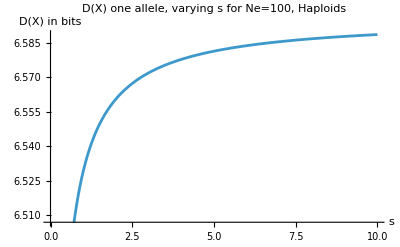

```mathematica
Quiet[(*many NIntegrate calls here*),NIntegrate::slwcon]
Plot[misoInf[100,s],{s,0.001,10},PlotLabel->"D(X) one allele, varying s for Ne=100, Haploids",AxesLabel->{"s","D(X) in bits"}]
```

```mathematica
Plot[misoInf[Ne,0.001],{Ne,10,10000},PlotLabel->"D(X) one allele varying Ne s=0.01, Haploids",AxesLabel->{"Ne","D(X) in bits"}]
Quiet[(*many NIntegrate calls here*),NIntegrate::slwcon]
```

Subdivide::sdmint: The number of subdivisions given in position 3 of Subdivide[0,1,10.2041] should be a positive machine-sized integer.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.99999999999999999999999999998369273566250875422125492455831169218}. NIntegrate obtained 137.404 and 19.3948 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.99999999999999999999999999998369273566250875422125492455831169218}. NIntegrate obtained 1. and 0.141152 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {1.0000000000000000000000000001500933888395083206533051021228150717}. NIntegrate obtained -0.936134-0.00600202 ⅈ and 0.128513 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

Part::partw: Part 4 of Subdivide[0,1,10.2041] does not exist.

Subdivide::sdmint: The number of subdivisions given in position 3 of Subdivide[0.,1.,10.2041] should be a positive machine-sized integer.

Part::partw: Part 4 of Subdivide[0.,1.,10.2041] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Subdivide::sdmint: The number of subdivisions given in position 3 of Subdivide[0.,1.,10.2041] should be a positive machine-sized integer.

General::stop: Further output of Subdivide::sdmint will be suppressed during this calculation.

NIntegrate::nlim: x = Subdivide[0.,1.,10.2041]⟦4⟧ is not a valid limit of integration.

NIntegrate::nlim: x = Subdivide[0.,1.,10.2041]⟦5⟧ is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

Part::pkspec1: The expression i cannot be used as a part specification.

Part::pkspec1: The expression 1+i cannot be used as a part specification.

Part::pkspec1: The expression i cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

$Aborted

#### Same with the free fitness for the Equilibrium

```mathematica
freeFitnessNS[Ne_?NumericQ,s_?NumericQ]:=Module[
{Z,rho,rhoTilde,V},
V[x_]:=-Ne Log[W[x,s]]+(1-2 Ne u) Log[x]+(1-2 Ne v) Log[1-x];
rhoTilde[x_]:=Exp[-V[x]];
Z=NIntegrate[rhoTilde[x],{x,0,1}];
rho[x_?NumericQ]:=rhoTilde[x]/Z;
freeFit= -NIntegrate[ rho[x]*V[x]/Ne,{x,0.000,1}]-1/Ne *NIntegrate[rho[x]*Log[rho[x]],{x,0.000,1}];
freeFit];
```

```mathematica
freeFitnessNS[100,0.1]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.99999999999999999999999999998369273566250875422125492455831169218}. NIntegrate obtained 620179. and 17423.7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.99999999999999999999999999998369273566250875422125492455831169218}. NIntegrate obtained -0.531536 and 0.0441081 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.99999999999999999999999999998369273566250875422125492455831169218}. NIntegrate obtained 39.8159 and 4.03613 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

0.133378

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.9999999831838662781447290697764483484444308913907661917619407177}. NIntegrate obtained 105.739 and 2.66308 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.99999999999999999999999999998369273566250875422125492455831169218}. NIntegrate obtained -0.212932 and 0.0208372 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.99999999999999833552297401554899705442790134545403187354907677264}. NIntegrate obtained 20.8902 and 3.15298 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

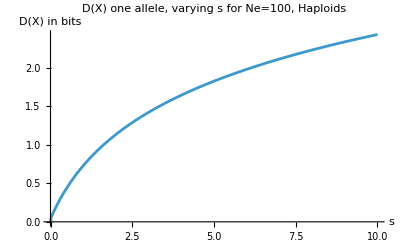

```mathematica
Plot[freeFitnessNS[100,s],{s,0.001,10},PlotLabel->"D(X) one allele, varying s for Ne=100, Haploids",AxesLabel->{"s","D(X) in bits"}]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.9999999831838662781447290697764483484444308913907661917619407177}. NIntegrate obtained 105.739 and 2.66308 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.99999999999999999999999999998369273566250875422125492455831169218}. NIntegrate obtained -0.212932 and 0.0208372 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.99999999999999833552297401554899705442790134545403187354907677264}. NIntegrate obtained 20.8902 and 3.15298 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

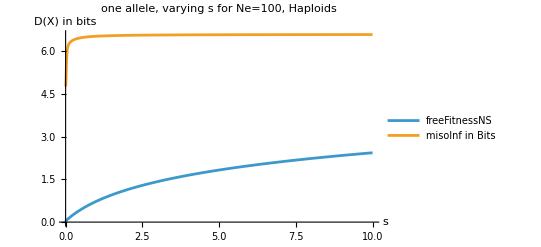

```mathematica
Plot[{freeFitnessNS[100,s],misoInf[100,s]},{s,0.001,10},PlotLegends->{"freeFitnessNS","misoInf in Bits"},PlotLabel->"one allele, varying s for Ne=100, Haploids",AxesLabel->{"s","D(X) in bits"}]
```